```mathematica
numberOfTrials = 0; 
probability = 1;
scorePerThrow = 1; 
results = List[];
iterator = 0; 
origBaseScore = 400; 

While [iterator < 1000, 
target =RandomInteger[{400,410}];
baseScore = origBaseScore;
ratio = target/origBaseScore; 
While [ target > baseScore ∧ baseScore > 0,
		If [ RandomInteger[1] == 0,
			baseScore = baseScore + scorePerThrow,
			baseScore  = baseScore - scorePerThrow];
		probability = probability * 0.9; 
	];
If [baseScore ≤0, 
	Print["ONE HIT"],
	AppendTo[results, {target,probability}]
];
probability = 1; 
iterator++; 
]
results;
```

ONE HIT

ONE HIT

ONE HIT

«8 more identical outputs»

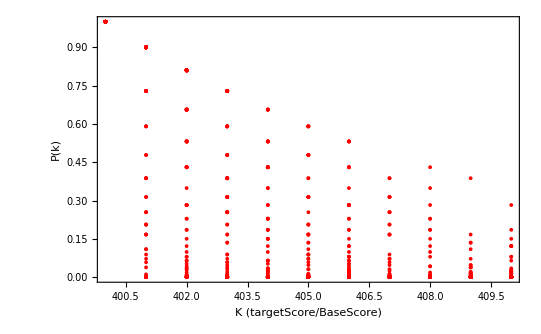

```mathematica
ListPlot[results,PlotRange->All,ImageSize->Large, Joined->False,Frame->True,FrameLabel->{"K (targetScore/BaseScore) ","P(k)","",""}, LabelStyle->{FontSize->14, Directive[Bold,Black]},PlotStyle->{RGBColor[1,0,0],PointSize[0.005]}]
```